# Лабораторная работа №13

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
    1 декабря 2021

```mathematica
(*объект точка на пл-ти*)
ClearAll[kmPoint];
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
kmPoint[{∅_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[∅],ρ Sin[∅]}];
kmPoint[id_String,{∅_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[∅],ρ Sin[∅]}];
kmPoint[km, id_String,___]["id"]:=If[id=="","Точка",id];
kmPoint[km,_String,coord_List,___]["coord"]:=coord;
NamedQ[kmPoint[km,id_String,___]]^:=id≠"";
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts];
kmPointShow[gp_List,opts___]:=Graphics[ReplaceAll[gp,P_kmPoint:>Tooltip[Point@P@"coord"]],Frame->True,GridLines->Automatic];
```

```mathematica
kmVector[id_String,coord:{_,_}]:=kmVector[km,id,coord];
kmVector[km, id_String,___]["id"]:=If[id=="","Вектор",id];
kmPoint[km,_String,coord_List,___]["coord"]:=coord;
kmVector[coord_List]:=kmVector[km,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[km,id,P1["coord"]-P0["coord"]];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[km,P1["coord"]-P0["coord"]];
kmVector[km,id_String,coord:{_,_}]["id"]:=id;
NamedQ[kmVector[km,id_String,___]]^:=id≠"";
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[If[And@@NamedQ/@{P0,P1},StringJoin[P0@"id",P1@"id"],""],P0,P1];
kmVector[km,id_String,coord:{_,_}]["coord"]:=coord;
kmVector[km,id___String,coord_List,___]["length"]:=√(#.#)&[kmVector[id,coord]["coord"]];
kmVector[km,_String,coord_List,___]["ort"]:=kmVector["",coord/(√(#.#)&[coord])];
kmVector[id_String,ort:{_,_},length_]:=kmVector[km,id,ort*length];
kmVector[ort:{_,_},length_]:=kmVector[km,"",ort*length];
```

## Задание 1

```mathematica
kmLine[km,id_String,{A_,B_,C_}]
```

kmLine[km,id_String,{A_,B_,C_}]

## Задание 2

Постройте булеву функцию NamedQ, позволяющую
определить, имеет ли представленный объект «прямая» имя .

```mathematica
NamedQ[kmLine[km,id_String,___]]^:=id≠"";
```

```mathematica
NamedQ[kmLine[km,"",___]]
```

False

```mathematica
NamedQ[kmLine[km,"AB",___]]
```

True

## Задание 3

```mathematica
kmLine[id_String,A_. x_+B_. y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[km,id,{A,B,C}]/;¬(*not*)PossibleZeroQ[Abs@A+Abs@B]
```

```mathematica
kmLine["L1",5 f-a==0,{f,a}]
```

kmLine[km,L1,{5,-1,0}]

```mathematica
kmLine["L1",5 f-a==0,{a,f}]
```

kmLine[km,L1,{-1,5,0}]

```mathematica
kmLine["L2",5 f==0,{f,a}](*в этом случае конструктор не отработал, т.к. уравнение прямой не соответсвует описанному образцу*)
```

kmLine[L2,5 f==0,{f,a}]

```mathematica
MatchQ[5 f==0,A_. x_+B_. y_+C_.==0]
```

False

```mathematica
MatchQ[5 f+9==0(*за 9 принимается y, а В - 1*),A_. x_+B_. y_+C_.==0]
```

True

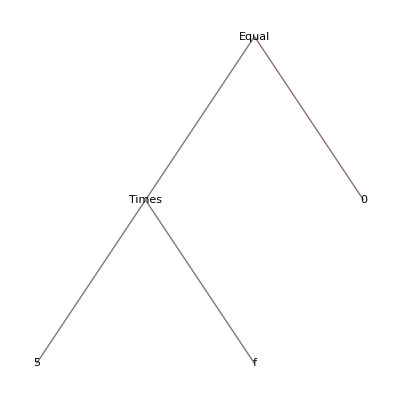

```mathematica
(5 f==0)//TreeForm
```

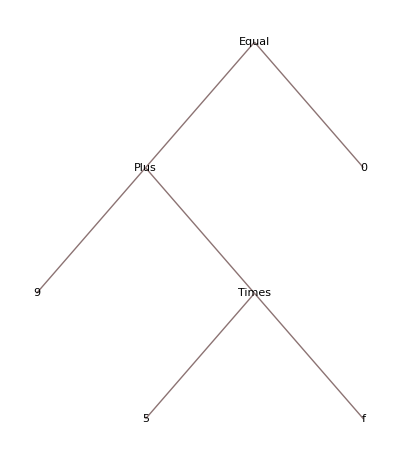

```mathematica
(5 f+9==0)//TreeForm
```

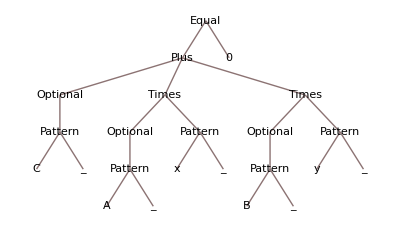

```mathematica
(A_. x_+B_. y_+C_.==0)//TreeForm
```

```mathematica
kmLine["L2",5 f+7==0,{f,a}]
```

kmLine[L2,7+5 f==0,{f,a}]

```mathematica
kmLine[id_String,A_. x_+C_.==0,{x_Symbol,_Symbol}]:=kmLine[km,id,{A,0,C}];
kmLine[id_String,B_. y_+C_.==0,{_Symbol,y_Symbol}]:=kmLine[km,id,{0,B,C}];
```

```mathematica
kmLine["L2",5 f+7==0,{f,a}]
```

kmLine[km,L2,{5,0,7}]

```mathematica
kmLine["L2",5 f==0,{f,a}]
```

kmLine[km,L2,{5,0,0}]

```mathematica
kmLine["L2",5 f==0,{a,f}]
```

kmLine[km,L2,{0,5,0}]

```mathematica
kmLine["L2",5==0,{f,a}]
```

kmLine[L2,False,{f,a}]

```mathematica
kmLine["L2",False,{f,a}]
```

kmLine[L2,False,{f,a}]

В последнем примере, первый аргумент после вычисления представлен символом False, он не удовлетворяет ни одному из образцов. Поэтому, укажем,что в представлении общего уравнения прямой по крайней мере один из коэффициентов при x или y должен быть отличен от нуля иначе вычисления должны быть прекращены.

```mathematica
kmLine[km,"",{A_,B_,_}]:=Abort[]/;PossibleZeroQ[Abs@A+Abs@B]
```

```mathematica
kmLine[km,"",{0,0.,3}]
```

$Aborted

## Задание 5

Обеспечьте возможность задания объекта «прямая на плоскости», указывая общее уравнение прямой .

```mathematica
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars]
```

```mathematica
kmLine[5 f+3==0,{f,a}]
```

kmLine[km,,{5,0,3}]

```mathematica
kmLine[5f==0,{f,b}]
```

kmLine[km,,{5,0,0}]

## Задание 6

Обеспечьте возможность задания объекта «прямая на плоскости» указанием точки, принадлежащей прямой, и направляющего вектора прямой, в случаях, когда прямая именована либо нет .

Способ 1. Построение общего уравнения прямой т вызов базового конструктора.

```mathematica
{P,P0}=kmPoint/@{{x,y},{p0x,p0y}}
```

{kmPoint[km,,{x,y}],kmPoint[km,,{p0x,p0y}]}

```mathematica
v=kmVector[{Vx,Vy}]
```

kmVector[km,,{Vx,Vy}]

```mathematica
{v@"coord",P@"coord"-P0@"coord"}//MatrixForm
```

(Vx | Vy
-p0x+x | -p0y+y)

```mathematica
Det[{v@"coord",P@"coord"-P0@"coord"}]==0 (*выражение,представляющее общее уравнение прямой в случае,когда она задана точкой p0 и направляющим вектором V, х и у - координаты произвольной точки, принадлежащей прямой*)
```

-p0y Vx+p0x Vy-Vy x+Vx y==0

```mathematica
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[id,Det[{Dir@"coord",{x,y}-P0@"coord"}]==0,{x,y}]
```

```mathematica
kmLine["L",kmPoint[{5,5}],kmVector[{-1,1}]]
```

kmLine[km,L,{-1,-1,10}]

Способ 2. Вычисление коэффициентов А, В, С общего уравнения прямой.

Анализируя -p0y Vx+p0x Vy-Vy x+Vx y==0, можно заметить, что A = - Vy, B = Vx, C = - p0y Vx + p0x Vy

```mathematica
({{0, -1}, {1, 0}}).v@"coord"(*нормальный вектор к прямой*)
```

{-Vy,Vx}

```mathematica
-(({{0, -1}, {1, 0}}).v@"coord").P0@"coord"
```

-p0y Vx+p0x Vy

```mathematica
Append[#,-#.P0@"coord"]&[({{0, -1}, {1, 0}}).v@"coord"](*получаем искомый список {A,B,C}*)
```

{-Vy,Vx,-p0y Vx+p0x Vy}

```mathematica
kmLine[id_String,P0_kmPoint,Dir_kmVector]:=kmLine[km,id,Append[#,-#.P0["coord"]]&[({{0, -1}, {1, 0}}).Dir["coord"]]](*Конструктор создает объект «прямая на плоскости» в случае,когда заданы имя прямой,точка,принадлежащая прямой и направляющий
вектор прямой*)
```

```mathematica
kmLine["",P0,v]
```

kmLine[km,,{-Vy,Vx,-p0y Vx+p0x Vy}]

```mathematica
kmLine["",kmPoint[{2,3}],kmVector[{10,20}]]
```

kmLine[km,,{-20,10,10}]

```mathematica
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[If[And@@(NamedQ/@{P,Dir}),StringJoin[P@"id",Dir@"id"],""],P,Dir]
```

```mathematica
kmLine[P0,v]
```

kmLine[km,,{-Vy,Vx,-p0y Vx+p0x Vy}]

```mathematica
P1=kmPoint["A",{Ax,Ay}]
```

kmPoint[km,A,{Ax,Ay}]

```mathematica
a=kmVector["a",{ax,ay}]
```

kmVector[km,a,{ax,ay}]

```mathematica
kmLine[P1,a]
```

kmLine[km,Aa,{-ay,ax,Ax ay-ax Ay}]

### Задание 7

Создайте конструкторы объекта «прямая на плоскости», если прямая l, именованная либо нет, задана двумя различными точками, ей принадлежащими .

```mathematica
ClearAll[P1,P2];
{P1,P2}=kmPoint/@{{5,4},{3,7}}
```

{kmPoint[km,,{5,4}],kmPoint[km,,{3,7}]}

```mathematica
kmVector[P1,P2]
```

kmVector[km,,{-2,3}]

```mathematica
kmLine[id_String,P1_kmPoint,P2_kmPoint]:=kmLine[id,P1,kmVector[P1,P2]]
```

```mathematica
kmLine["AC",P1,P2]
```

kmLine[km,AC,{-3,-2,23}]

```mathematica
kmLine[P1_kmPoint,P2_kmPoint]:=kmLine["",P1,kmVector[P1,P2]]
```

```mathematica
kmLine[P1,P2]
```

kmLine[km,,{-3,-2,23}]

### Задание 8

```mathematica
vect=kmVector[{2,5}]
```

kmVector[km,,{2,5}]

```mathematica
vectL=kmVector[({{0, -1}, {1, 0}}).vect@"coord"]
```

kmVector[km,,{-5,2}]

```mathematica
vectR=kmVector[-({{0, -1}, {1, 0}}).vect@"coord"]
```

kmVector[km,,{5,-2}]

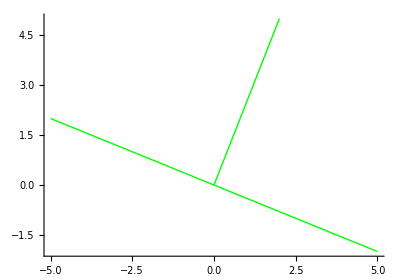

```mathematica
Show[Graphics[{Green,Line[{{0,0},#@"coord"}&/@{vect,vectL,vectR}]}, Axes->True]]
```

### Задание 9

Представьте в Mathematica лево ориентированную
нормаль NL к прямой l, если задан направляющий вектор V прямой l.

```mathematica
V=kmVector[{Vx,Vy}]
```

kmVector[km,,{Vx,Vy}]

```mathematica
({{0, -1}, {1, 0}}).V@"coord"
```

{-Vy,Vx}

```mathematica
Nleft=kmVector[({{0, -1}, {1, 0}}).V@"coord"]
```

kmVector[km,,{-Vy,Vx}]

### Задание 10

Представьте в Mathematica направляющий вектор V
прямой l, если задана лево ориентированная по отношению к вектору V нормаль NL к прямой l

```mathematica
Nleft1=kmVector[{Nx,Ny}]
```

kmVector[km,,{Nx,Ny}]

```mathematica
({{0, 1}, {-1, 0}}).Nleft1@"coord"
```

{Ny,-Nx}

```mathematica
V1=kmVector[({{0, 1}, {-1, 0}}).Nleft1@"coord"]
```

kmVector[km,,{Ny,-Nx}]

### Задание 11

Создайте возможность задания прямой l на плоскости указанием координат точки, ей принадлежащей, и координат нормального вектора к этой прямой . Прямая может быть именована либо нет .

```mathematica
kmLine[id_String,P0_kmPoint,N_kmVector,"norm"]:=kmLine[id,P0,kmVector[({{0, 1}, {-1, 0}}).N@"coord"]]
```

```mathematica
kmLine["AC",kmPoint[{3,5}],kmVector[{5,6}],"norm"]
```

kmLine[km,AC,{5,6,-45}]

```mathematica
kmLine[P0_kmPoint,N_kmVector,"norm"]:=kmLine["",P0,kmVector[({{0, 1}, {-1, 0}}).N@"coord"]]
```

```mathematica
kmLine[kmPoint[{3,5}],kmVector[{5,6}],"norm"]
```

kmLine[km,,{5,6,-45}]

### Задание 12

Напишите оператор, возвращающий имя объекта
«прямая на плоскости», если оно существует, и нарицательное имя "Прямая" в противном случае .

```mathematica
kmLine[km, id_String,___]["id"]:=If[id=="","Прямая",id];
```

```mathematica
kmLine[P1,a]["id"]
```

Прямая

```mathematica
kmLine[P0,v]["id"]
```

Прямая

### Задание 13

Напишите оператор, возвращающий список коэффициентов общего уравнения прямой .

```mathematica
kmLine[km,_String,coef:{A_,B_,C_},___]["coef"]:=coef
```

```mathematica
kmLine["line",kmPoint[{8,1}],kmPoint[{1,9}]]["coef"]
```

{-8,-7,71}

### Задание 14

Напишите оператор, возвращающий общее уравнение прямой.

```mathematica
kmLine[km,___,coef:{A_,B_,C_},___]["equ"]:=coef.{x,y,1}
```

```mathematica
kmLine[km,"",{-8,-7,71}]["equ"]
```

71-8 x-7 y

### Задание 15

Напишите оператор, возвращающий нормальный вектор прямой .

```mathematica
kmLine[km,___,{A_,B_,C_}]["normal"]:=kmVector["",{A,B}]@"coord"
```

```mathematica
kmLine[km,"",{9,8,3}]["normal"]
```

{9,8}

### Задание 16

Напишите оператор, возвращающий направляющий вектор прямой .

```mathematica
kmLine[km,___,{A_,B_,C_}]["vect"]:=kmVector["",{-B,A}]@"coord"
```

```mathematica
kmLine[km,"",{9,8,3}]["vect"]
```

{-8,9}

### Задание 17

Постройте функцию, которая для заданной прямой на плоскости, вычисляет координаты двух различных точек, принадлежащих этой прямой.

```mathematica
L=kmLine[km,"",{17,-8,-10}]
```

kmLine[km,,{17,-8,-10}]

```mathematica
L@"coef".{x0,y,1}==0(*Вычислим координаты некоторой точки,принадлежащей заданной
прямой*)
```

-10-8 y+17 x0==0

```mathematica
First@Solve[L@"coef".{x0,y,1}==0,y]
```

{y→1/8 (-10+17 x0)}

```mathematica
{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0,y](*формируем из полученной пары искомый список координат точки,принадлежащей прямой*)
```

{x0,1/8 (-10+17 x0)}

```mathematica
Table[{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0,y],{x0,{-1,1}}](*Чтобы получить две различные точки прямой,зафиксируем два различных значения координаты x: x0=-1 и x0=1*)
```

{{-1,-27/8},{1,7/8}}

```mathematica
Table[{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0],{x0,{-1,1}}](*последнее выражение можно записать,не указывая имя переменной,относительно которой Solve решает уравнение,т.к.уравнение содержит только одну переменную,после того как переменной
x последовательно задаются значения x0=-1 и x0=1*)
```

{{-1,-27/8},{1,7/8}}

```mathematica
Ly=kmLine[km,"",{0,-8,-10}]
```

kmLine[km,,{0,-8,-10}]

```mathematica
Table[{x0,y}/.First@Solve[Ly@"coef".{x0,y,1}==0],{x0,{-1,1}}]
```

{{-1,-5/4},{1,-5/4}}

Когда коэф. при у равен 0, этот метод не работает: при фиксировании  оставшейся единственной переменной x правая часть уравнения прямой  становится числом, и само уравнение вырождается в логическое высказывание.

```mathematica
Lx=kmLine[km,"",{17,0,-10}]
```

kmLine[km,,{17,0,-10}]

```mathematica
Lx@"coef"
```

{17,0,-10}

```mathematica
{17,0,-10}.{1,y,1}==0
```

False

```mathematica
Lx@"coef".{1,y,1}==0
```

False

В случае, когда коэффициент при переменной y равен нулю, мы можем использовать такой же прием, но фиксировать координату y = y0 .

```mathematica
L["coef"]
```

{17,-8,-10}

```mathematica
L["coef"][[{1,2}]]
```

{17,-8}

```mathematica
If[Apply[Less,Abs@L["coef"][[{1,2}]]],Table[{x0,y}/.First@Solve[L@"coef".{x0,y,1}==0],{x0,{-1,1}}], Table[{x,y0}/.First@Solve[L@"coef".{x,y0,1}==0],{y0,{-1,1}}]]
```

{{2/17,-1},{18/17,1}}

Функция kmGetTwoLinePoints  для заданной прямой возвращает две различные точки, принадлежащие этой прямой.

```mathematica
ClearAll[kmGetTwoLinePoints];
kmGetTwoLinePoints[line_kmLine]:=Map[kmPoint,If[Apply[Less,Abs@line["coef"][[{1,2}]]],Table[{x,y}/.First@Solve[L@"coef".{x,y,1}==0],{x,{-1,1}}], Table[{x,y}/.First@Solve[L@"coef".{x,y,1}==0],{y,{-1,1}}]]]
```

```mathematica
kmGetTwoLinePoints[L]
```

{kmPoint[km,,{2/17,-1}],kmPoint[km,,{18/17,1}]}

### Задание 18

Обучите Mathematica отображать на рисунке объект «точка на плоскости» и объект «прямая на плоскости». Используйте правила локальных преобразований.

```mathematica
ClearAll[ kmGraphics2D];
kmGraphics2D [gp_List,opts___]:=Graphics[
ReplaceAll[ gp,{P_kmPoint:> Tooltip[Point@P@ "coord",Style[Format[P,StandardForm],Large]],L_kmLine:> Tooltip[InfiniteLine@Through@kmGetTwoLinePoints [L]@ "coord",Style[Format[L,StandardForm],Large]]}],opts]
```

```mathematica
ClearAll[P1,P2,P3,L1,L2];
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
{L1,L2}=kmLine[km,"",#]&/@{{1,5,3},{2,3,1}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

{kmLine[km,,{1,5,3}],kmLine[km,,{2,3,1}]}

```mathematica
L1
```

kmLine[km,,{1,5,3}]

```mathematica
L2
```

kmLine[km,,{2,3,1}]

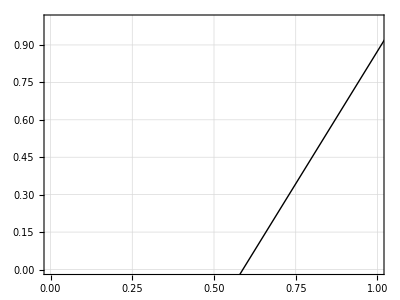

```mathematica
kmGraphics2D[{L1},Frame-> True, GridLines-> Automatic, PlotRange-> All]
```

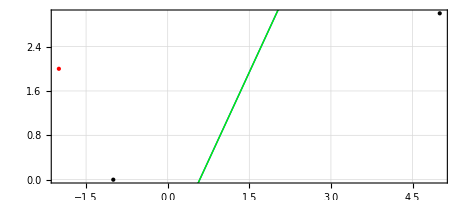

```mathematica
kmGraphics2D[{{PointSize@Large,P1,P2,Red,P3},
{Thick,Blue,L1,Green,L2}},
Frame-> True, GridLines-> Automatic, PlotRange-> All]
```